```mathematica
(* MACROPARASITE (H. polygyrus) MEAN BURDENS *)
```

```mathematica
(* Turn off Solve warning messages *)
Off[Solve::ratnz]

(* Function to generate table of mean burdens for ρ=0 and ρ=1, for all θ1 and θ2 combinations *)
provchange[pars_]:=
Module[{data},
data= Table[Table[Solve[system/.pars//.provpars,{p,l,h,hpolymb}][[1]],{prov,0,1}],{θ1,0,5},{θ2,0,5}];
Table[(hpolymb/.data[[i]][[j]][[2]])-(hpolymb/.data[[i]][[j]][[1]]),{i,1,6},{j,1,6}]
]

(* Provisioning response calculations *)
provpars={β1min->0.205/2,β1max->0.205,β2min->1*^-3,β2max->2*^-3,β1p->β1min+(β1max-β1min)*E^(-θ1*prov), β2p->β2max-(β2max-β2min)*E^(-θ2*prov)};

(* System equations *)
system={b*h*(K-h)/K-μ*h-ν*p==0&&β1p*β2p*l*h-(μ+ν+ϵ)*p-p^2*ν*(k+1)/(h*k)==0&&τ*p-ϕ*l==0 &&p/h == hpolymb};
```

```mathematica
(* GENERATE PLOTS VARYING BY K *)

(* Compile parameter lists *)
pars1={K ->42.12, τ->42,b->1.24, μ->1/13.75,ν->0.765,ϵ->0,k->0.1,ϕ->1/8,β->0.0001409278};
pars2={K ->42.12*1.5, τ->42,b->1.24, μ->1/13.75,ν->0.765,ϵ->0,k->0.1,ϕ->1/8,β->0.0001409278};
pars3={K ->42.12*2, τ->42,b->1.24, μ->1/13.75,ν->0.765,ϵ->0,k->0.1,ϕ->1/8,β->0.0001409278};

(* Generate tables of differences in predicted mean burdens for all θ1 and θ2 combinations *)
diffhpolymb1 =provchange[pars1]
diffhpolymb2 =provchange[pars2]
diffhpolymb3 =provchange[pars3]
```

{{0.,0.133769,0.1765,0.191468,0.196878,0.198856},{-0.0786608,0.0267872,0.0617411,0.0741364,0.0786361,0.0802834},{-0.109973,-0.0175037,0.0136149,0.0247069,0.0287409,0.0302188},{-0.121842,-0.0345584,-0.00501408,0.0055377,0.00937796,0.0107852},{-0.126258,-0.0409408,-0.0119996,-0.00165557,0.00211009,0.00349008},{-0.127889,-0.0433037,-0.0145878,-0.00432138,-0.000583629,0.000786189}}

{{0.,0.16342,0.21314,0.230287,0.236451,0.238699},{-0.102001,0.0337075,0.0769364,0.0920651,0.0975315,0.0995292},{-0.143907,-0.0223029,0.0171958,0.0311079,0.036146,0.0379889},{-0.159994,-0.0442482,-0.00636625,0.00701012,0.0118586,0.0136326},{-0.166007,-0.0525158,-0.0152658,-0.00210004,0.00267372,0.00442062},{-0.168232,-0.0555843,-0.018572,-0.00548566,-0.00074009,0.000996566}}

{{0.,0.180979,0.233901,0.25193,0.258384,0.260734},{-0.118763,0.0382423,0.0865814,0.103314,0.109337,0.111535},{-0.168926,-0.0255736,0.0195702,0.0353103,0.0409902,0.043065},{-0.1884,-0.0509501,-0.00727774,0.00799348,0.0135097,0.0155255},{-0.195711,-0.0605658,-0.017481,-0.00239877,0.00305129,0.0050432},{-0.198421,-0.0641424,-0.0212804,-0.00627002,-0.000845149,0.00113766}}

-0.2

0.3

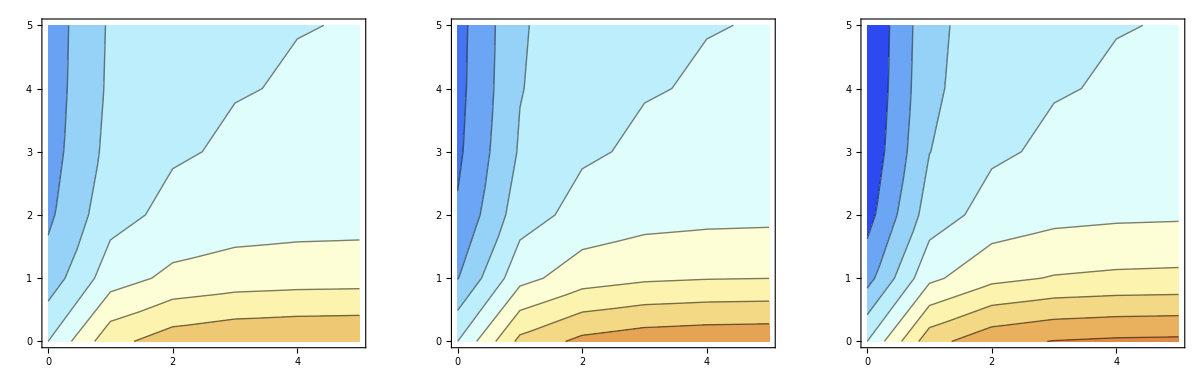

```mathematica
(* Calculate min and max values across all diffhpolymb arrays, rounding up/down to nearest value to 1 decimal place *)
(* Note, these scale within the above 3 generated plots; to scale across all parasites would need to calculate min and maxvals across them all *)
minvals=Floor[Min[diffhpolymb1,diffhpolymb2,diffhpolymb3]*10]/10//N
maxvals=Ceiling[Max[diffhpolymb1,diffhpolymb2,diffhpolymb3]*10]/10//N

(* Now create all 3 graphs, using the same common min and max values *)
p1=ListContourPlot[diffhpolymb1,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p2=ListContourPlot[diffhpolymb2,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p3=ListContourPlot[diffhpolymb3,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
Show[GraphicsGrid[{{p1,p2,p3}}]]

(* Create a legend spanning specified range (minvals to maxvals) *)
BarLegend[{"LightTemperatureMap",{minvals,maxvals}}]
```

```mathematica
(* GENERATE PLOTS VARYING BY b *)

(* Compile parameter lists *)
pars1={K ->42.12, τ->42,b->1.24, μ->1/13.75,ν->0.765,ϵ->0,k->0.1,ϕ->1/8,β->0.0001409278};
pars2={K ->42.12, τ->42,b->1.24*1.5, μ->1/13.75,ν->0.765,ϵ->0,k->0.1,ϕ->1/8,β->0.0001409278};
pars3={K ->42.12, τ->42,b->1.24*2, μ->1/13.75,ν->0.765,ϵ->0,k->0.1,ϕ->1/8,β->0.0001409278};

(* Generate tables of differences in predicted mean burdens for all θ1 and θ2 combinations *)
diffhpolymb1 =provchange[pars1]
diffhpolymb2 =provchange[pars2]
diffhpolymb3 =provchange[pars3]
```

{{0.,0.133769,0.1765,0.191468,0.196878,0.198856},{-0.0786608,0.0267872,0.0617411,0.0741364,0.0786361,0.0802834},{-0.109973,-0.0175037,0.0136149,0.0247069,0.0287409,0.0302188},{-0.121842,-0.0345584,-0.00501408,0.0055377,0.00937796,0.0107852},{-0.126258,-0.0409408,-0.0119996,-0.00165557,0.00211009,0.00349008},{-0.127889,-0.0433037,-0.0145878,-0.00432138,-0.000583629,0.000786189}}

{{0.,0.155284,0.20687,0.225177,0.231824,0.234258},{-0.0871581,0.0303666,0.0705312,0.0849236,0.0901679,0.0920904},{-0.121041,-0.0196519,0.0153898,0.0279956,0.0325953,0.0342824},{-0.133767,-0.0386567,-0.00564475,0.00624858,0.0105907,0.0121836},{-0.138485,-0.0457328,-0.0134884,-0.00186517,0.00237918,0.00393634},{-0.140226,-0.0483476,-0.0163884,-0.00486565,-0.000657672,0.000886193}}

{{0.,0.168083,0.225172,0.245586,0.253018,0.255742},{-0.0919415,0.0324333,0.0756542,0.0912322,0.0969203,0.0990072},{-0.127232,-0.0208784,0.016411,0.0298933,0.0348219,0.0366308},{-0.140422,-0.0409869,-0.00600593,0.00665677,0.0112877,0.0129877},{-0.145303,-0.0484534,-0.0143396,-0.00198531,0.00253356,0.00419246},{-0.147103,-0.0512096,-0.0174173,-0.00517741,-0.000700122,0.000943549}}

-0.2

0.3

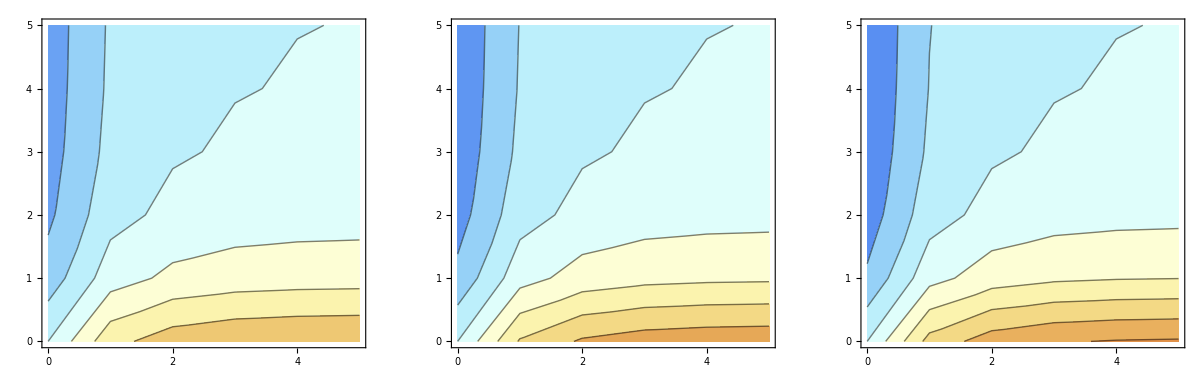

```mathematica
(* Calculate min and max values across all resprev arrays, rounding up/down to nearest value to 1 decimal place *)
(* Note, these scale within the above 3 generated plots; to scale across all parasites would need to calculate min and maxvals across them all *)
minvals=Floor[Min[diffhpolymb1,diffhpolymb2,diffhpolymb3]*10]/10//N
maxvals=Ceiling[Max[diffhpolymb1,diffhpolymb2,diffhpolymb3]*10]/10//N

(* Now create all 3 graphs, using the same common min and max values *)
p1=ListContourPlot[diffhpolymb1,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p2=ListContourPlot[diffhpolymb2,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p3=ListContourPlot[diffhpolymb3,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
Show[GraphicsGrid[{{p1,p2,p3}}]]

(* Create a legend spanning specified range (minvals to maxvals) *)
BarLegend[{"LightTemperatureMap",{minvals,maxvals}}]
```

```mathematica
(* GENERATE PLOTS VARYING BY μ *)

(* Compile parameter lists *)
pars1={K ->42.12, τ->42,b->1.24, μ->1/13.75,ν->0.765,ϵ->0,k->0.1,ϕ->1/8,β->0.0001409278};
pars2={K ->42.12, τ->42,b->1.24, μ->1/13.75/1.5,ν->0.765,ϵ->0,k->0.1,ϕ->1/8,β->0.0001409278};
pars3={K ->42.12, τ->42,b->1.24, μ->1/13.75/2,ν->0.765,ϵ->0,k->0.1,ϕ->1/8,β->0.0001409278};

(* Generate tables of differences in predicted mean burdens for all θ1 and θ2 combinations *)
diffhpolymb1 =provchange[pars1]
diffhpolymb2 =provchange[pars2]
diffhpolymb3 =provchange[pars3]
```

{{0.,0.133769,0.1765,0.191468,0.196878,0.198856},{-0.0786608,0.0267872,0.0617411,0.0741364,0.0786361,0.0802834},{-0.109973,-0.0175037,0.0136149,0.0247069,0.0287409,0.0302188},{-0.121842,-0.0345584,-0.00501408,0.0055377,0.00937796,0.0107852},{-0.126258,-0.0409408,-0.0119996,-0.00165557,0.00211009,0.00349008},{-0.127889,-0.0433037,-0.0145878,-0.00432138,-0.000583629,0.000786189}}

{{0.,0.13614,0.179628,0.194862,0.200368,0.20238},{-0.080055,0.027262,0.0628354,0.0754504,0.0800298,0.0817063},{-0.111922,-0.017814,0.0138562,0.0251448,0.0292504,0.0307544},{-0.124002,-0.035171,-0.00510295,0.00563585,0.00954418,0.0109763},{-0.128496,-0.0416664,-0.0122123,-0.00168492,0.00214748,0.00355194},{-0.130156,-0.0440712,-0.0148463,-0.00439797,-0.000593974,0.000800123}}

{{0.,0.137326,0.181193,0.196558,0.202112,0.204142},{-0.0807521,0.0274994,0.0633825,0.0761074,0.0807267,0.0824178},{-0.112897,-0.0179691,0.0139769,0.0253638,0.0295051,0.0310222},{-0.125082,-0.0354772,-0.00514739,0.00568493,0.00962729,0.0110719},{-0.129615,-0.0420293,-0.0123186,-0.00169959,0.00216618,0.00358287},{-0.131289,-0.044455,-0.0149756,-0.00443627,-0.000599146,0.000807091}}

-0.2

0.3

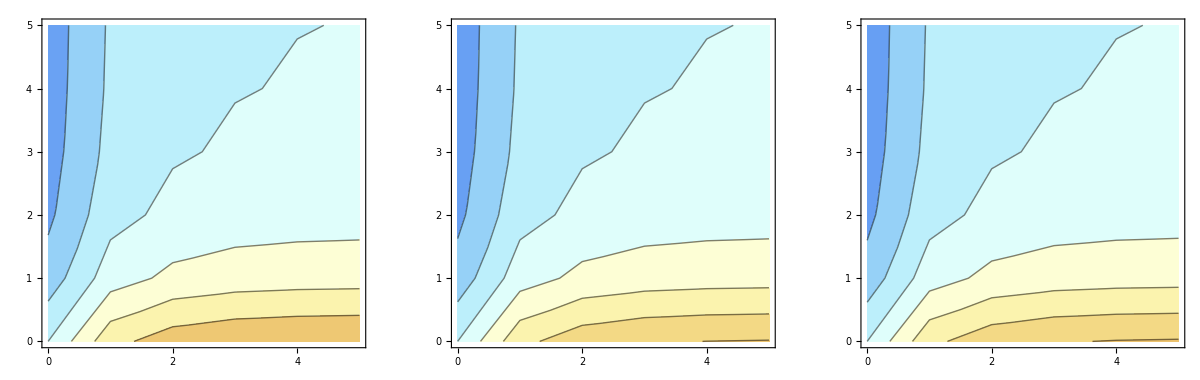

```mathematica
(* Calculate min and max values across all resprev arrays, rounding up/down to nearest value to 1 decimal place *)
(* Note, these scale within the above 3 generated plots; to scale across all parasites would need to calculate min and maxvals across them all *)
minvals=Floor[Min[diffhpolymb1,diffhpolymb2,diffhpolymb3]*10]/10//N
maxvals=Ceiling[Max[diffhpolymb1,diffhpolymb2,diffhpolymb3]*10]/10//N

(* Now create all 3 graphs, using the same common min and max values *)
p1=ListContourPlot[diffhpolymb1,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p2=ListContourPlot[diffhpolymb2,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p3=ListContourPlot[diffhpolymb3,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
Show[GraphicsGrid[{{p1,p2,p3}}]]

(* Create a legend spanning specified range (minvals to maxvals) *)
BarLegend[{"LightTemperatureMap",{minvals,maxvals}}]
```